```mathematica
(*Метод средних ячеек Log[Cx*dx^2+Cy*dy^2]
Область D: 1≤x≤3; 2≤y≤5
f(x)=x^2+y^2
Сгущение сеток:
*)
f[x_,y_]:=x^3+y^3;
a=1;b=3;c=2;d=5;
func1[dx_,dy_]:=Sum[Sum[f[(2*x+dx)/2,(2*y+dy)/2]*dx*dy,{y,c,d,dy}]//N,{x,a,b,dx}];
ErrorList={};
ValueList={};
Module[{dx=(b-a)/100,dy=(d-c)/100},
Do[
AppendTo[ValueList,{dx,func1[dx, dy]}];
dx=dx/2//N;
dy=dy/2//N; 
Cx=1/24*Integrate[f[b,y]-f[a,y],{y,c,d}]//N;
Cy=1/24*Integrate[f[x,d]-f[x,c],{x,a,b}]//N;
AppendTo[ErrorList,{Log[(b-a)/dx//N],Log[(d-c)/dy//N],Last[ValueList][[2]]-729/2}];
,{i,1,5}];
];
```

{{1/50,377.435},{0.01,370.925},{0.005,367.702},{0.0025,366.098},{0.00125,365.298}}

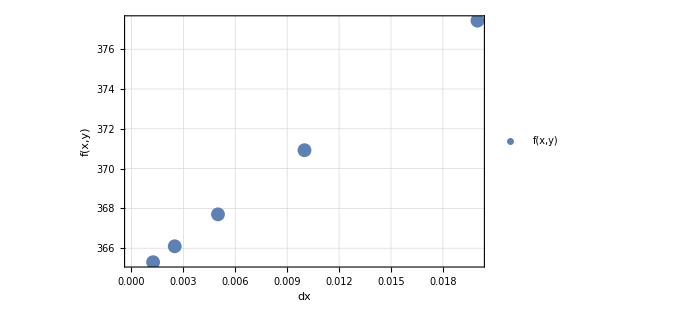

-Graphics3D-

```mathematica
ValueList
ListPlot[ValueList,PlotLegends->Placed[{Style["f(x,y)",20,Black,FontFamily->"Cambria"]},Right],FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["dx",20,Black,FontFamily->"Cambria"],Style["f(x,y)",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{Automatic,Automatic}]
Show[ListPointPlot3D[ErrorList,PlotStyle->PointSize[Large]],Axes->True,AxesLabel->{Style["Log[nkx]",15,Black,FontFamily->"Cambria"],Style["Log[nky]",15,Black,FontFamily->"Cambria"],Style["Delta",15,Black,FontFamily->"Cambria"]},
FaceGridsStyle->Directive[Darker[Gray]],
LabelStyle->Directive[15,Black,FontFamily->"Cambria"],ImageSize->300]
```

```mathematica
(*
Квазиравномерные секти
*)
a=0;b=10;c=0;d=5;
f2[x_,y_]:=√(x*y);
xold=Table[x,{x,a,b,1/100}];
yold=Table[y,{y,c,d,1/100}];
xlist=Table[a+(b-a)*(E^(0.1*x)-1)/(E^0.1-1)//N,{x,0,1,1/10}];
ylist=Table[c+(d-c)*(E^(0.1*y)-1)/(E^0.1-1)//N,{y,0,1,1/10}];

Sum[Sum[
f2[(xlist[[i+1]]+xlist[[i]])/2,(ylist[[j+1]]+ylist[[j]])/2]*(xlist[[i+1]]-xlist[[i]])*(ylist[[j+1]]-ylist[[j]]),
{i,1,Length[xlist]-1}]//N,{j,1,Length[ylist]-1}]
```

157.905

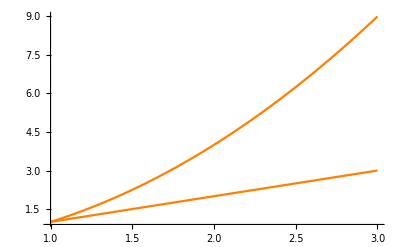

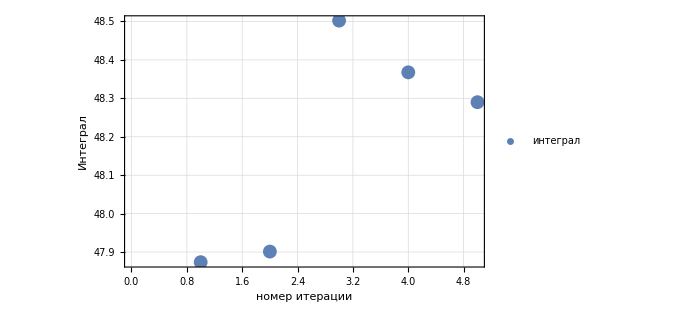

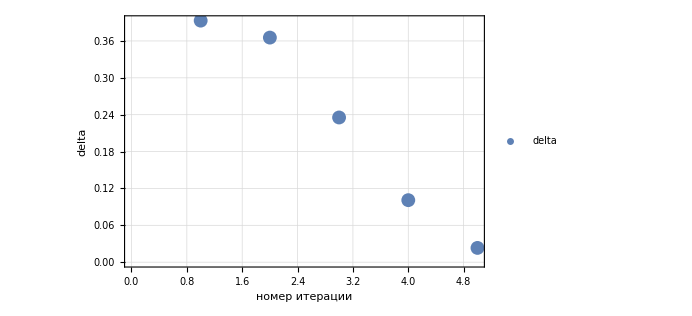

```mathematica
(*Криволинейные области
1≤x≤3
x≤y≤x^2
*)
a=1;b=3;c=1;d=9;
f3[x_,y_]:=Piecewise[{{x^2+y,1≤x≤3&&x≤y≤x^2},{0,x>3},{0,x<1}}];
Show[Plot[x,{x,a,b},PlotStyle->Orange],Plot[x^2,{x,a,b},PlotStyle->Orange],PlotRange->{{a,b},{c,d}}]
func2[dx_,dy_]:=Sum[Sum[f3[(2*x+dx)/2,(2*y+dy)/2]*dx*dy,{y,c,d,dy}]//N,{x,a,b,dx}];
ValueList1={};
ValueList2={};
hx=(b-a)/10;hy=(d-c)/10;
Do[
AppendTo[ValueList1,Abs[func2[hx, hy]-724/15]];
AppendTo[ValueList2,Abs[func2[hx, hy]]];
hx=hx/2//N;
hy=hy/2//N; 
,{i,1,5}];
ListPlot[ValueList2,PlotLegends->Placed[{Style["интеграл",20,Black,FontFamily->"Cambria"]},Right],FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["номер итерации",20,Black,FontFamily->"Cambria"],Style["Интеграл",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{Automatic,Automatic}]
ListPlot[ValueList1,PlotLegends->Placed[{Style["delta",20,Black,FontFamily->"Cambria"]},Right],FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["номер итерации",20,Black,FontFamily->"Cambria"],Style["delta",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{Automatic,Automatic}]
```

```mathematica
(*Произведение квадратурных формул*)
n=4;
f33[x_,y_]:=y^2+x;
yclist=Table[Cos[(Pi*(i+1))/(n+1)],{i,0,n-1}]
clist={(Pi*(5-√5))/40,(Pi*(5+√5))/40,(Pi*(5+√5))/40,(Pi*(5-√5))/40}
a=-1;
b=1;
cp[y_]:=y;
dp[y_]:=y^2;
pols=Table[Simplify[1/(2^n*n!)*D[(x^2-1)^n,{x,n }]],{n,2,5,1}];
knots=Table[
Solve[pols[[n]]==0,x]
,{n,1,4,1}];
wn=Table[Product[x-knots[[n]][[k]][[1]][[2]],{k,1,n+1}],{n,1,4,1}];
coef=Table[
Table[
(NIntegrate[(wn[[n]]/(x-knots[[n]][[i]][[1]][[2]]))^2,{x,-1,1}]//N)/(((wn[[n]]/(x-knots[[n]][[i]][[1]][[2]]))^2)/.{x->knots[[n]][[i]][[1]][[2]]})
,{i,1,Length[knots[[n]]],1}]
,{n,1,4,1}];

vals=Table[(dp[ylist[[j]]]-cp[ylist[[j]]])/2*
Sum[coef[[n-1]][[i]]*f33[(dp[ylist[[j]]]-cp[ylist[[j]]])/2* knots[[n-1]][[i]][[1]][[2]]+(dp[ylist[[j]]]+cp[ylist[[j]]])/2,ylist[[j]]],{i,1,n,1}],{j,1,Length[yclist]}]
Sum[vals[[i]]*clist[[i]]/(√Abs[(b-ylist[[i]])*(a-ylist[[i]])]),{i,1,4}]
```

{1/4 (1+√5),1/4 (-1+√5),1/4 (1-√5),1/4 (-1-√5)}

{1/40 (5-√5) π,1/40 (5+√5) π,1/40 (5+√5) π,1/40 (5-√5) π}

{0.,-0.145049,-0.0708736,2.5084}

0.281644

48.2667

49.7114

100

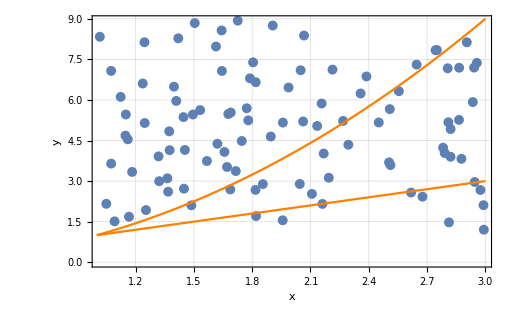

```mathematica
(*Метод Монте-Карло*)
Clear[ResultL]
724/15//N
functt[x_,y_]:=Piecewise[{{x^2+y,1≤x≤3&&x≤y≤x^2},{0,x>3},{0,x<1}}];
a=1;
b=3;
c=1;
d=9;
n=10000;
PointList={};
ResultL={};
MonteCarloDoubleIntegral[f_,a_,b_,c_,d_,k_]:=
Module[{x,y,z,area,count},area=(b-a)*(d-c);count=0;Do[x=RandomReal[{a,b}];y=RandomReal[{c,d}];
AppendTo[PointList,{x,y}];
z=f[x,y];
If[1≤y≤9,AppendTo[ResultL,z];count++],{k} ];
Print[Mean[ResultL]*area];Print[count]]

MonteCarloDoubleIntegral[functt,a,b,c,d,100]

Show[ListPlot[PointList,FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["x",20,Black,FontFamily->"Cambria"],Style["y",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{Automatic,Automatic}],Plot[x,{x,a,b},PlotStyle->{Orange,Large}],Plot[x^2,{x,a,b},PlotStyle->{Orange,Large}]]
```